```mathematica
Remove["Global`*"];
ClearAll["Global`*"];
```

```mathematica
data=ReadList["C:\\Users\\Christopher Plumberg\\Downloads\\lowT.dat",Real];
data=ArrayReshape[data,{Length[data]/5,5}];
data={data[[;;,1;;4]],data[[;;,5]]}//Transpose;
```

```mathematica
Tmin=30;
f=Interpolation[data,InterpolationOrder->4,Method->"Hermite"];
fp[T_,μB_,μQ_,μS_]:=Evaluate[D[f[T,μB,μQ,μS], T]];
fpp[T_,μB_,μQ_,μS_]:=Evaluate[D[f[T,μB,μQ,μS], T,T]];
g[T_,μB_,μQ_,μS_]:=Piecewise[{{f[Tmin,μB,μQ,μS]Log[2,T/Tmin+1],T≤Tmin},{f[T,μB,μQ,μS],T>Tmin}}];
g2[T_,μB_,μQ_,μS_]:=Piecewise[{{f0 Exp[a1 (1-(Tmin/T))+a2 (1-(Tmin/T)^2)]//.{a1->(Tmin (3 f0 fp0-fp0^2 Tmin+f0 fpp0 Tmin))/f0^2,a2->(-2 f0 fp0 Tmin+fp0^2 Tmin^2-f0 fpp0 Tmin^2)/(2 f0^2),f0->f[Tmin,μB,μQ,μS],fp0->fp[Tmin,μB,μQ,μS],fpp0->fpp[Tmin,μB,μQ,μS]},T≤Tmin},{f[T,μB,μQ,μS],T>Tmin}}];
g2[T_,μB_,μQ_,μS_]:=Piecewise[{{f[Tmin,μB,μQ,μS]Exp[a1 (1-(Tmin/T)^2)]//.{a1->(fp0 Tmin)/(2 f0),f0->f[Tmin,μB,μQ,μS],fp0->fp[Tmin,μB,μQ,μS]},T≤Tmin},{f[T,μB,μQ,μS],T>Tmin}}];
(*g3[T_,μB_,μQ_,μS_]:=Piecewise[{{f[Tmin,μB,μQ,μS] Exp[a1 (1-(Tmin/T)^2)(1+a2(T/Tmin)^2)]//.{a1->(15 (f0 fp0+30 fp0^2-30 f0 fpp0))/(4 f0^2+10^-100),a2->(3 (f0 fp0-10 fp0^2+10 f0 fpp0))/(f0 fp0+30 fp0^2-30 f0 fpp0+10^-100),f0->f[Tmin,μB,μQ,μS],fp0->fp[Tmin,μB,μQ,μS],fpp0->fpp[Tmin,μB,μQ,μS]},T≤Tmin},{f[T,μB,μQ,μS],T>Tmin}}];
g4[T_,μB_,μQ_,μS_]:=Piecewise[{{f[Tmin,μB,μQ,μS] Exp[a1 (1-(Tmin/T)^2)(1+a2(T/Tmin)^2+a3(T/Tmin)^4)]//.{a1->(15 (f0^2 fp0+30 f0 fp0^2+600 fp0^3-30 f0^2 fpp0-900 f0 fp0 fpp0+300 f0^2 fppp0))/(8 f0^3+10^-100),a2->(8 (f0^2 fp0-150 fp0^3+225 f0 fp0 fpp0-75 f0^2 fppp0))/(f0^2 fp0+30 f0 fp0^2+600 fp0^3-30 f0^2 fpp0-900 f0 fp0 fpp0+300 f0^2 fppp0+10^-100),a3->(-f0^2 fp0-30 f0 fp0^2+600 fp0^3+30 f0^2 fpp0-900 f0 fp0 fpp0+300 f0^2 fppp0)/(f0^2 fp0+30 f0 fp0^2+600 fp0^3-30 f0^2 fpp0-900 f0 fp0 fpp0+300 f0^2 fppp0+10^-100),f0->f[Tmin,μB,μQ,μS],fp0->fp[Tmin,μB,μQ,μS],fpp0->fpp[Tmin,μB,μQ,μS],fppp0->fppp[Tmin,μB,μQ,μS]},T≤Tmin},{f[T,μB,μQ,μS],T>Tmin}}];*)
p[T_,μB_,μQ_,μS_]:=T^4 g[T,μB,μQ,μS];
s[T_,μB_,μQ_,μS_]:=Evaluate[D[p[T,μB,μQ,μS], T]];
ρB[T_,μB_,μQ_,μS_]:=Evaluate[D[p[T,μB,μQ,μS], μB]];
ρQ[T_,μB_,μQ_,μS_]:=Evaluate[D[p[T,μB,μQ,μS], μQ]];
ρS[T_,μB_,μQ_,μS_]:=Evaluate[D[p[T,μB,μQ,μS], μS]];
e[T_,μB_,μQ_,μS_]:=T s[T,μB,μQ,μS]+μB ρB[T,μB,μQ,μS]+μQ ρQ[T,μB,μQ,μS]+μS ρS[T,μB,μQ,μS]-p[T,μB,μQ,μS];
χTT[T_,μB_,μQ_,μS_]:=Evaluate[D[p[T,μB,μQ,μS], T,T]];
χTμB[T_,μB_,μQ_,μS_]:=Evaluate[D[p[T,μB,μQ,μS], T,μB]];
χTμQ[T_,μB_,μQ_,μS_]:=Evaluate[D[p[T,μB,μQ,μS], T,μQ]];
χTμS[T_,μB_,μQ_,μS_]:=Evaluate[D[p[T,μB,μQ,μS], T,μS]];
χμBμB[T_,μB_,μQ_,μS_]:=Evaluate[D[p[T,μB,μQ,μS], μB,μB]];
χμBμQ[T_,μB_,μQ_,μS_]:=Evaluate[D[p[T,μB,μQ,μS], μB,μQ]];
χμBμS[T_,μB_,μQ_,μS_]:=Evaluate[D[p[T,μB,μQ,μS], μB,μS]];
χμQμQ[T_,μB_,μQ_,μS_]:=Evaluate[D[p[T,μB,μQ,μS], μQ,μQ]];
χμQμS[T_,μB_,μQ_,μS_]:=Evaluate[D[p[T,μB,μQ,μS], μQ,μS]];
χμSμS[T_,μB_,μQ_,μS_]:=Evaluate[D[p[T,μB,μQ,μS], μS,μS]];
χ[T_,μB_,μQ_,μS_]:={{χTT[T,μB,μQ,μS],χTμB[T,μB,μQ,μS],χTμQ[T,μB,μQ,μS],χTμS[T,μB,μQ,μS]},{χTμB[T,μB,μQ,μS],χμBμB[T,μB,μQ,μS],χμBμQ[T,μB,μQ,μS],χμBμS[T,μB,μQ,μS]},{χTμQ[T,μB,μQ,μS],χμBμQ[T,μB,μQ,μS],χμQμQ[T,μB,μQ,μS],χμQμS[T,μB,μQ,μS]},{χTμS[T,μB,μQ,μS],χμBμS[T,μB,μQ,μS],χμQμS[T,μB,μQ,μS],χμSμS[T,μB,μQ,μS]}};
χp[T_,μB_,μQ_,μS_]:=χ[T,μB,μQ,μS]*{T,μB,μQ,μS};
cs2[T_,μB_,μQ_,μS_]:=Module[{dT,dμB,dμQ,dμS,solϵ,solB,solQ,solS,term1,term2,term3,term4,χ0,χp0,e0,p0,s0,ρB0,ρQ0,ρS0},
χ0=χ[T,μB,μQ,μS];
χp0=χp[T,μB,μQ,μS];
e0=e[T,μB,μQ,μS];
p0=p[T,μB,μQ,μS];
s0=s[T,μB,μQ,μS];
ρB0=ρB[T,μB,μQ,μS];
ρQ0=ρQ[T,μB,μQ,μS];
ρS0=ρS[T,μB,μQ,μS];
solϵ=Solve[#==0&/@(χ0[[2;;4]].{dT,dμB,dμQ,dμS}),{dμB,dμQ,dμS}]//Flatten;
solB=Solve[{Total[χp0.{dT,dμB,dμQ,dμS}]==0,(χ0[[3]].{dT,dμB,dμQ,dμS})==0,(χ0[[4]].{dT,dμB,dμQ,dμS})==0},{dT,dμQ,dμS}]//Flatten;
solQ=Solve[{Total[χp0.{dT,dμB,dμQ,dμS}]==0,(χ0[[2]].{dT,dμB,dμQ,dμS})==0,(χ0[[4]].{dT,dμB,dμQ,dμS})==0},{dT,dμQ,dμS}]//Flatten;
solS=Solve[{Total[χp0.{dT,dμB,dμQ,dμS}]==0,(χ0[[2]].{dT,dμB,dμQ,dμS})==0,(χ0[[3]].{dT,dμB,dμQ,dμS})==0},{dT,dμQ,dμS}]//Flatten;
term1=(dT s0+dμB ρB0+dμQ ρQ0+dμS ρS0/.solϵ)/(dT 10^-100+Total[χp0.{dT,dμB,dμQ,dμS}/.solϵ])//FullSimplify;term2=(ρB0/(e0+p0+10^-100))(dT s0+dμB ρB0+dμQ ρQ0+dμS ρS0/.solB)/(dμB 10^-100+(χ0[[2]].{dT,dμB,dμQ,dμS})/.solB)//FullSimplify;term3=(ρQ0/(e0+p0+10^-100))(dT s0+dμB ρB0+dμQ ρQ0+dμS ρS0/.solQ)/(dμQ 10^-100+(χ0[[3]].{dT,dμB,dμQ,dμS})/.solQ)//FullSimplify;term4=(ρS0/(e0+p0+10^-100))(dT s0+dμB ρB0+dμQ ρQ0+dμS ρS0/.solS)/(dμS 10^-100+(χ0[[4]].{dT,dμB,dμQ,dμS})/.solS)//FullSimplify;
(*{solϵ,solB,solQ,solS,term1,term2,term3,term4,term1+term2+term3+term4}*)
term1+term2+term3+term4
];
(*cs2[T_,μB_,μQ_,μS_]:=Module[{dT,dμB,dμQ,dμS,solϵ,solB,solQ,solS,den,χTT0,χTμB0,χTμQ0,χTμS0,χμBμB0,χμBμQ0,χμBμS0,χμQμQ0,χμQμS0,χμSμS0,e0,p0,s0,ρB0,ρQ0,ρS0},
e0=e[T,μB,μQ,μS];
p0=p[T,μB,μQ,μS];
s0=s[T,μB,μQ,μS];
ρB0=ρB[T,μB,μQ,μS];
ρQ0=ρQ[T,μB,μQ,μS];
ρS0=ρS[T,μB,μQ,μS];
{χTT0,χTμB0,χTμQ0,χTμS0,χμBμB0,χμBμQ0,χμBμS0,χμQμQ0,χμQμS0,χμSμS0}={χTT[T,μB,μQ,μS],χTμB[T,μB,μQ,μS],χTμQ[T,μB,μQ,μS],χTμS[T,μB,μQ,μS],χμBμB[T,μB,μQ,μS],χμBμQ[T,μB,μQ,μS],χμBμS[T,μB,μQ,μS],χμQμQ[T,μB,μQ,μS],χμQμS[T,μB,μQ,μS],χμSμS[T,μB,μQ,μS]};
den=((T (χTμQ0^2 χμBμS0^2-χTT0 χμBμS0^2 χμQμQ0+χTμS0^2 (χμBμQ0^2-χμBμB0 χμQμQ0)-2 χTμB0 χTμQ0 χμBμS0 χμQμS0+2 χTT0 χμBμQ0 χμBμS0 χμQμS0+χTμB0^2 χμQμS0^2-χTT0 χμBμB0 χμQμS0^2+2 χTμS0 (-χTμQ0 χμBμQ0 χμBμS0+χTμB0 χμBμS0 χμQμQ0+χTμQ0 χμBμB0 χμQμS0-χTμB0 χμBμQ0 χμQμS0)-(χTμQ0^2 χμBμB0-2 χTμB0 χTμQ0 χμBμQ0+χTT0 χμBμQ0^2+χTμB0^2 χμQμQ0-χTT0 χμBμB0 χμQμQ0) χμSμS0)));
{ρB0 χTμS0 χμBμS0 χμQμQ0-s0 χμBμS0^2 χμQμQ0-ρB0 χTμS0 χμBμQ0 χμQμS0-ρB0 χTμQ0 χμBμS0 χμQμS0+2 s0 χμBμQ0 χμBμS0 χμQμS0+ρB0 χTμB0 χμQμS0^2-s0 χμBμB0 χμQμS0^2+ρS0 (-χTμQ0 χμBμQ0 χμBμS0+χTμB0 χμBμS0 χμQμQ0+χTμS0 (χμBμQ0^2-χμBμB0 χμQμQ0)+χTμQ0 χμBμB0 χμQμS0-χTμB0 χμBμQ0 χμQμS0)+ρB0 χTμQ0 χμBμQ0 χμSμS0-s0 χμBμQ0^2 χμSμS0-ρB0 χTμB0 χμQμQ0 χμSμS0+s0 χμBμB0 χμQμQ0 χμSμS0+ρQ0 (-χTμS0 χμBμQ0 χμBμS0+χTμQ0 χμBμS0^2+χTμS0 χμBμB0 χμQμS0-χTμB0 χμBμS0 χμQμS0-χTμQ0 χμBμB0 χμSμS0+χTμB0 χμBμQ0 χμSμS0),1/(e0+p0)ρB0 (T (-ρB0 χTμS0^2 χμQμQ0+s0 χTμS0 χμBμS0 χμQμQ0+2 ρB0 χTμQ0 χTμS0 χμQμS0-s0 χTμS0 χμBμQ0 χμQμS0-s0 χTμQ0 χμBμS0 χμQμS0-ρB0 χTT0 χμQμS0^2+s0 χTμB0 χμQμS0^2+ρS0 (χTμQ0^2 χμBμS0+χTμB0 χTμS0 χμQμQ0-χTT0 χμBμS0 χμQμQ0+χTT0 χμBμQ0 χμQμS0-χTμQ0 (χTμS0 χμBμQ0+χTμB0 χμQμS0))-ρB0 χTμQ0^2 χμSμS0+s0 χTμQ0 χμBμQ0 χμSμS0+ρB0 χTT0 χμQμQ0 χμSμS0-s0 χTμB0 χμQμQ0 χμSμS0+ρQ0 (χTμS0^2 χμBμQ0+χTT0 χμBμS0 χμQμS0-χTμS0 (χTμQ0 χμBμS0+χTμB0 χμQμS0)+χTμB0 χTμQ0 χμSμS0-χTT0 χμBμQ0 χμSμS0))+μB (-ρB0 χTμS0 χμBμS0 χμQμQ0+s0 χμBμS0^2 χμQμQ0+ρB0 χTμS0 χμBμQ0 χμQμS0+ρB0 χTμQ0 χμBμS0 χμQμS0-2 s0 χμBμQ0 χμBμS0 χμQμS0-ρB0 χTμB0 χμQμS0^2+s0 χμBμB0 χμQμS0^2+ρS0 (-χTμS0 χμBμQ0^2+χTμQ0 χμBμQ0 χμBμS0+χTμS0 χμBμB0 χμQμQ0-χTμB0 χμBμS0 χμQμQ0-χTμQ0 χμBμB0 χμQμS0+χTμB0 χμBμQ0 χμQμS0)+(-ρB0 χTμQ0 χμBμQ0+s0 χμBμQ0^2+ρB0 χTμB0 χμQμQ0-s0 χμBμB0 χμQμQ0) χμSμS0+ρQ0 (χTμS0 χμBμQ0 χμBμS0-χTμQ0 χμBμS0^2-χTμS0 χμBμB0 χμQμS0+χTμB0 χμBμS0 χμQμS0+χTμQ0 χμBμB0 χμSμS0-χTμB0 χμBμQ0 χμSμS0))),1/(e0+p0)ρQ0 (T (ρB0 χTμS0^2 χμBμQ0-ρB0 χTμQ0 χTμS0 χμBμS0-s0 χTμS0 χμBμQ0 χμBμS0+s0 χTμQ0 χμBμS0^2-ρB0 χTμB0 χTμS0 χμQμS0+s0 χTμS0 χμBμB0 χμQμS0+ρB0 χTT0 χμBμS0 χμQμS0-s0 χTμB0 χμBμS0 χμQμS0+ρS0 (χTμQ0 χTμS0 χμBμB0-χTμB0 χTμS0 χμBμQ0-χTμB0 χTμQ0 χμBμS0+χTT0 χμBμQ0 χμBμS0+χTμB0^2 χμQμS0-χTT0 χμBμB0 χμQμS0)+(ρB0 χTμB0 χTμQ0-s0 χTμQ0 χμBμB0-ρB0 χTT0 χμBμQ0+s0 χTμB0 χμBμQ0) χμSμS0-ρQ0 (χTμS0^2 χμBμB0-2 χTμB0 χTμS0 χμBμS0+χTT0 χμBμS0^2+χTμB0^2 χμSμS0-χTT0 χμBμB0 χμSμS0))+μQ (-ρB0 χTμS0 χμBμS0 χμQμQ0+s0 χμBμS0^2 χμQμQ0+ρB0 χTμS0 χμBμQ0 χμQμS0+ρB0 χTμQ0 χμBμS0 χμQμS0-2 s0 χμBμQ0 χμBμS0 χμQμS0-ρB0 χTμB0 χμQμS0^2+s0 χμBμB0 χμQμS0^2+ρS0 (-χTμS0 χμBμQ0^2+χTμQ0 χμBμQ0 χμBμS0+χTμS0 χμBμB0 χμQμQ0-χTμB0 χμBμS0 χμQμQ0-χTμQ0 χμBμB0 χμQμS0+χTμB0 χμBμQ0 χμQμS0)+(-ρB0 χTμQ0 χμBμQ0+s0 χμBμQ0^2+ρB0 χTμB0 χμQμQ0-s0 χμBμB0 χμQμQ0) χμSμS0+ρQ0 (χTμS0 χμBμQ0 χμBμS0-χTμQ0 χμBμS0^2-χTμS0 χμBμB0 χμQμS0+χTμB0 χμBμS0 χμQμS0+χTμQ0 χμBμB0 χμSμS0-χTμB0 χμBμQ0 χμSμS0))),1/(den(e0+p0))ρS0 (T (-ρB0 χTμQ0 χTμS0 χμBμQ0+s0 χTμS0 χμBμQ0^2+ρB0 χTμQ0^2 χμBμS0-s0 χTμQ0 χμBμQ0 χμBμS0+ρB0 χTμB0 χTμS0 χμQμQ0-s0 χTμS0 χμBμB0 χμQμQ0-ρB0 χTT0 χμBμS0 χμQμQ0+s0 χTμB0 χμBμS0 χμQμQ0-ρS0 (χTμQ0^2 χμBμB0-2 χTμB0 χTμQ0 χμBμQ0+χTT0 χμBμQ0^2+χTμB0^2 χμQμQ0-χTT0 χμBμB0 χμQμQ0)-ρB0 χTμB0 χTμQ0 χμQμS0+s0 χTμQ0 χμBμB0 χμQμS0+ρB0 χTT0 χμBμQ0 χμQμS0-s0 χTμB0 χμBμQ0 χμQμS0+ρQ0 (χTμQ0 χTμS0 χμBμB0-χTμB0 χTμS0 χμBμQ0-χTμB0 χTμQ0 χμBμS0+χTT0 χμBμQ0 χμBμS0+χTμB0^2 χμQμS0-χTT0 χμBμB0 χμQμS0))+μS (-ρB0 χTμS0 χμBμS0 χμQμQ0+s0 χμBμS0^2 χμQμQ0+ρB0 χTμS0 χμBμQ0 χμQμS0+ρB0 χTμQ0 χμBμS0 χμQμS0-2 s0 χμBμQ0 χμBμS0 χμQμS0-ρB0 χTμB0 χμQμS0^2+s0 χμBμB0 χμQμS0^2+ρS0 (-χTμS0 χμBμQ0^2+χTμQ0 χμBμQ0 χμBμS0+χTμS0 χμBμB0 χμQμQ0-χTμB0 χμBμS0 χμQμQ0-χTμQ0 χμBμB0 χμQμS0+χTμB0 χμBμQ0 χμQμS0)+(-ρB0 χTμQ0 χμBμQ0+s0 χμBμQ0^2+ρB0 χTμB0 χμQμQ0-s0 χμBμB0 χμQμQ0) χμSμS0+ρQ0 (χTμS0 χμBμQ0 χμBμS0-χTμQ0 χμBμS0^2-χTμS0 χμBμB0 χμQμS0+χTμB0 χμBμS0 χμQμS0+χTμQ0 χμBμB0 χμSμS0-χTμB0 χμBμQ0 χμSμS0)))}//Total
];*)
```

```mathematica
quants=Flatten[Table[{T-10^-6,μB,μQ,μS,T^-4 p[T,μB,μQ,μS],T^-3 s[T,μB,μQ,μS],T^-3 ρB[T,μB,μQ,μS],T^-3 ρS[T,μB,μQ,μS],T^-3 ρQ[T,μB,μQ,μS],T^-4 e[T,μB,μQ,μS],cs2[T,μB,μQ,μS]},{T,10^-6,26,5},{μB,-450,450,50},{μQ,-450,450,50},{μS,-450,450,50}],3]//Quiet;
derivs=Flatten[Table[{T-10^-6,μB,μQ,μS,T^-2{χμBμB[T,μB,μQ,μS],χμQμQ[T,μB,μQ,μS],χμSμS[T,μB,μQ,μS],χμBμQ[T,μB,μQ,μS],χμBμS[T,μB,μQ,μS],χμQμS[T,μB,μQ,μS],χTμB[T,μB,μQ,μS],χTμQ[T,μB,μQ,μS],χTμS[T,μB,μQ,μS],χTT[T,μB,μQ,μS]}}//Flatten,{T,10^-6,26,5},{μB,-450,450,50},{μQ,-450,450,50},{μS,-450,450,50}],3]//Quiet;
```

```mathematica
Export[NotebookDirectory[]<>"extrapolated_EoS_quantities.dat",quants//N]
Export[NotebookDirectory[]<>"extrapolated_EoS_derivatives.dat",derivs//N]
```

C:\Users\Christopher Plumberg\Desktop\Research\UIUC\BSQ\EoS_BQS_Derivatives\extrapolated_EoS_quantities.dat

C:\Users\Christopher Plumberg\Desktop\Research\UIUC\BSQ\EoS_BQS_Derivatives\extrapolated_EoS_derivatives.dat

```mathematica
cs2[30,50,50,50]//AbsoluteTiming
```

{0.0192795,0.283788}

```mathematica
cs2[29.7,50,50,50]
```

0.283578

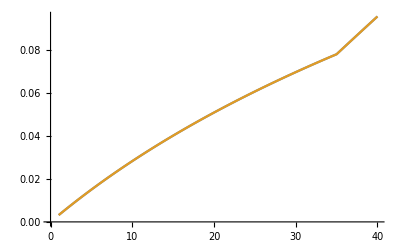

```mathematica
ListLinePlot[{quants[[;;,{1,5}]],Table[{T,T^-4 p[T,50,50,50]},{T,1,40,1/5}]},PlotRange->All,AxesOrigin->{0,0}]//Quiet
```

```mathematica
30^-2 χ[30,50,50,50]//MatrixForm
```

(1.57039 | -0.000175951 | 0.205932 | -0.000398486
-0.000175951 | 0.0000526131 | 0.0000283761 | -0.0000169551
0.205932 | 0.0000283761 | 0.0425711 | 0.000111952
-0.000398486 | -0.0000169551 | 0.000111952 | 9.73709×10^-6)

```mathematica
sol=Solve[#==0&/@(35^2 χ[35,50,50,50][[2;;4]].{dT,dμB,dμQ,dμS}),{dμB,dμQ,dμS}]//Flatten
```

{dμB→-0.518852 dT,dμQ→-4.04147 dT,dμS→-11.3041 dT}

```mathematica
(dT s[35,50,50,50]+dμB ρB[35,50,50,50]+dμQ ρQ[35,50,50,50]+dμS ρS[35,50,50,50]/.sol)/Total[35^2 χp[35,50,50,50].{dT,dμB,dμQ,dμS}/.sol]//FullSimplify
```

0.000185821

```mathematica
Table[Subscript[χ, a,b],{a,{T,μB,μQ,μS}},{b,{T,μB,μQ,μS}}].{dT,dμB,dμQ,dμS}//MatrixForm
```

(dT χ_(T,T)+dμB χ_(T,μB)+dμQ χ_(T,μQ)+dμS χ_(T,μS)
dT χ_(μB,T)+dμB χ_(μB,μB)+dμQ χ_(μB,μQ)+dμS χ_(μB,μS)
dT χ_(μQ,T)+dμB χ_(μQ,μB)+dμQ χ_(μQ,μQ)+dμS χ_(μQ,μS)
dT χ_(μS,T)+dμB χ_(μS,μB)+dμQ χ_(μS,μQ)+dμS χ_(μS,μS))

```mathematica
sol=Solve[(Table[Subscript[χ, a,b],{a,{T,μB}},{b,{T,μB}}][[2]].{dT,dμB})==0,dμB]//First
dpdϵ==(dT s+dμB ρB/.sol)/Total[(Table[a Subscript[χ, a,b],{a,{T,μB}},{b,{T,μB}}].{dT,dμB})/.sol]//FullSimplify
```

{dμB→-(dT χ_(μB,T))/(χ_(μB,μB))}

dpdϵ==(ρB χ_(μB,T)-s χ_(μB,μB))/(T χ_(T,μB) χ_(μB,T)-T χ_(T,T) χ_(μB,μB))

```mathematica
sol2=Solve[#==0&/@(Table[Subscript[χ, a,b],{a,{T,μB,μQ,μS}},{b,{T,μB,μQ,μS}}][[2;;4]].{dT,dμB,dμQ,dμS}),{dμB,dμQ,dμS}]//Flatten//FullSimplify
dpdϵ==(dT s+dμB ρB+dμQ ρQ+dμS ρS/.sol2)/Total[(Table[a Subscript[χ, a,b],{a,{T,μB,μQ,μS}},{b,{T,μB,μQ,μS}}].{dT,dμB,dμQ,dμS})/.sol2]//FullSimplify
```

{dμB→(dT (χ_(μB,μS) (χ_(μQ,μQ) χ_(μS,T)-χ_(μQ,T) χ_(μS,μQ))+χ_(μB,μQ) (-χ_(μQ,μS) χ_(μS,T)+χ_(μQ,T) χ_(μS,μS))+χ_(μB,T) (χ_(μQ,μS) χ_(μS,μQ)-χ_(μQ,μQ) χ_(μS,μS))))/(χ_(μB,μS) (-χ_(μQ,μQ) χ_(μS,μB)+χ_(μQ,μB) χ_(μS,μQ))+χ_(μB,μQ) (χ_(μQ,μS) χ_(μS,μB)-χ_(μQ,μB) χ_(μS,μS))+χ_(μB,μB) (-χ_(μQ,μS) χ_(μS,μQ)+χ_(μQ,μQ) χ_(μS,μS))),dμQ→(dT (χ_(μB,μS) (-χ_(μQ,μB) χ_(μS,T)+χ_(μQ,T) χ_(μS,μB))+χ_(μB,μB) (χ_(μQ,μS) χ_(μS,T)-χ_(μQ,T) χ_(μS,μS))+χ_(μB,T) (-χ_(μQ,μS) χ_(μS,μB)+χ_(μQ,μB) χ_(μS,μS))))/(χ_(μB,μS) (-χ_(μQ,μQ) χ_(μS,μB)+χ_(μQ,μB) χ_(μS,μQ))+χ_(μB,μQ) (χ_(μQ,μS) χ_(μS,μB)-χ_(μQ,μB) χ_(μS,μS))+χ_(μB,μB) (-χ_(μQ,μS) χ_(μS,μQ)+χ_(μQ,μQ) χ_(μS,μS))),dμS→(dT (χ_(μB,μQ) (χ_(μQ,μB) χ_(μS,T)-χ_(μQ,T) χ_(μS,μB))+χ_(μB,μB) (-χ_(μQ,μQ) χ_(μS,T)+χ_(μQ,T) χ_(μS,μQ))+χ_(μB,T) (χ_(μQ,μQ) χ_(μS,μB)-χ_(μQ,μB) χ_(μS,μQ))))/(χ_(μB,μS) (-χ_(μQ,μQ) χ_(μS,μB)+χ_(μQ,μB) χ_(μS,μQ))+χ_(μB,μQ) (χ_(μQ,μS) χ_(μS,μB)-χ_(μQ,μB) χ_(μS,μS))+χ_(μB,μB) (-χ_(μQ,μS) χ_(μS,μQ)+χ_(μQ,μQ) χ_(μS,μS)))}

dpdϵ==(-ρS χ_(μB,μB) χ_(μQ,μQ) χ_(μS,T)+ρQ χ_(μB,μB) χ_(μQ,μS) χ_(μS,T)+ρS χ_(μB,T) χ_(μQ,μQ) χ_(μS,μB)-ρQ χ_(μB,T) χ_(μQ,μS) χ_(μS,μB)+ρS χ_(μB,μB) χ_(μQ,T) χ_(μS,μQ)-ρS χ_(μB,T) χ_(μQ,μB) χ_(μS,μQ)+ρB χ_(μB,T) χ_(μQ,μS) χ_(μS,μQ)-s χ_(μB,μB) χ_(μQ,μS) χ_(μS,μQ)+χ_(μB,μS) (χ_(μQ,μQ) (ρB χ_(μS,T)-s χ_(μS,μB))+χ_(μQ,μB) (-ρQ χ_(μS,T)+s χ_(μS,μQ))+χ_(μQ,T) (ρQ χ_(μS,μB)-ρB χ_(μS,μQ)))+(χ_(μB,μB) (-ρQ χ_(μQ,T)+s χ_(μQ,μQ))+χ_(μB,T) (ρQ χ_(μQ,μB)-ρB χ_(μQ,μQ))) χ_(μS,μS)+χ_(μB,μQ) (χ_(μQ,μS) (-ρB χ_(μS,T)+s χ_(μS,μB))+χ_(μQ,μB) (ρS χ_(μS,T)-s χ_(μS,μS))+χ_(μQ,T) (-ρS χ_(μS,μB)+ρB χ_(μS,μS))))/(T (χ_(T,μB) χ_(μB,μS) χ_(μQ,μQ) χ_(μS,T)-χ_(T,μB) χ_(μB,μQ) χ_(μQ,μS) χ_(μS,T)-χ_(T,T) χ_(μB,μS) χ_(μQ,μQ) χ_(μS,μB)+χ_(T,T) χ_(μB,μQ) χ_(μQ,μS) χ_(μS,μB)-χ_(T,μB) χ_(μB,μS) χ_(μQ,T) χ_(μS,μQ)+χ_(T,T) χ_(μB,μS) χ_(μQ,μB) χ_(μS,μQ)+χ_(T,μB) χ_(μB,T) χ_(μQ,μS) χ_(μS,μQ)-χ_(T,T) χ_(μB,μB) χ_(μQ,μS) χ_(μS,μQ)+χ_(T,μS) (χ_(μQ,μQ) (-χ_(μB,μB) χ_(μS,T)+χ_(μB,T) χ_(μS,μB))+χ_(μB,μQ) (χ_(μQ,μB) χ_(μS,T)-χ_(μQ,T) χ_(μS,μB))+(χ_(μB,μB) χ_(μQ,T)-χ_(μB,T) χ_(μQ,μB)) χ_(μS,μQ))+(χ_(T,μB) (χ_(μB,μQ) χ_(μQ,T)-χ_(μB,T) χ_(μQ,μQ))+χ_(T,T) (-χ_(μB,μQ) χ_(μQ,μB)+χ_(μB,μB) χ_(μQ,μQ))) χ_(μS,μS)+χ_(T,μQ) (χ_(μQ,μS) (χ_(μB,μB) χ_(μS,T)-χ_(μB,T) χ_(μS,μB))+χ_(μB,μS) (-χ_(μQ,μB) χ_(μS,T)+χ_(μQ,T) χ_(μS,μB))+(-χ_(μB,μB) χ_(μQ,T)+χ_(μB,T) χ_(μQ,μB)) χ_(μS,μS))))

```mathematica
35^-2 χ[35,50,50,50]//Flatten//DeleteDuplicates
```

{1.90444,-0.000222964,0.2376,0.00175421,0.0000309408,0.0000186726,-0.0000278201,0.0586347,0.0000548779,0.00013684}

```mathematica
fp[T_,μB_,μQ_,μS_]:=Evaluate[D[f[T,μB,μQ,μS], T]];
fpp[T_,μB_,μQ_,μS_]:=Evaluate[D[f[T,μB,μQ,μS], T,T]];
fppp[T_,μB_,μQ_,μS_]:=Evaluate[D[f[T,μB,μQ,μS], T,T,T]];
g2[T_,μB_,μQ_,μS_]:=Piecewise[{{f[Tmin,μB,μQ,μS]Exp[a1 (1-(Tmin/T)^2)]//.{a1->(15 fp0)/f0,f0->f[Tmin,μB,μQ,μS],fp0->fp[Tmin,μB,μQ,μS]},T<Tmin},{f[T,μB,μQ,μS],T≥Tmin}}];
g3[T_,μB_,μQ_,μS_]:=Piecewise[{{f[Tmin,μB,μQ,μS] Exp[a1 (1-(Tmin/T)^2)(1+a2(T/Tmin)^4)]//.{a1->(75 (f0 fp0+6 fp0^2-6 f0 fpp0))/(8 f0^2),a2->(3 (f0 fp0-10 fp0^2+10 f0 fpp0))/(5 (f0 fp0+6 fp0^2-6 f0 fpp0)),f0->f[Tmin,μB,μQ,μS],fp0->fp[Tmin,μB,μQ,μS],fpp0->fpp[Tmin,μB,μQ,μS]},T≤Tmin},{f[T,μB,μQ,μS],T>Tmin}}];
g4[T_,μB_,μQ_,μS_]:=Piecewise[{{f[Tmin,μB,μQ,μS] Exp[a1 (1-(Tmin/T)^2)(1+a2(T/Tmin)^2+a3(T/Tmin)^4)]//.{a1->(15 (f0^2 fp0+30 f0 fp0^2+600 fp0^3-30 f0^2 fpp0-900 f0 fp0 fpp0+300 f0^2 fppp0))/(8 f0^3),a2->(8 (f0^2 fp0-150 fp0^3+225 f0 fp0 fpp0-75 f0^2 fppp0))/(f0^2 fp0+30 f0 fp0^2+600 fp0^3-30 f0^2 fpp0-900 f0 fp0 fpp0+300 f0^2 fppp0),a3->(-f0^2 fp0-30 f0 fp0^2+600 fp0^3+30 f0^2 fpp0-900 f0 fp0 fpp0+300 f0^2 fppp0)/(f0^2 fp0+30 f0 fp0^2+600 fp0^3-30 f0^2 fpp0-900 f0 fp0 fpp0+300 f0^2 fppp0),f0->f[Tmin,μB,μQ,μS],fp0->fp[Tmin,μB,μQ,μS],fpp0->fpp[Tmin,μB,μQ,μS],fppp0->fppp[Tmin,μB,μQ,μS]},T≤Tmin},{f[T,μB,μQ,μS],T>Tmin}}];
```

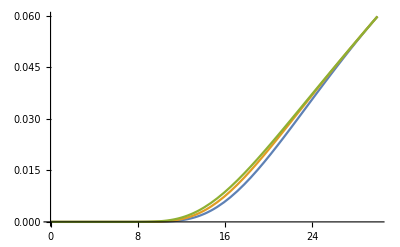

```mathematica
Plot[{g2[T,50,50,50],g3[T,50,50,50],g4[T,50,50,50]},{T,0,30}]//Quiet
```

```mathematica
D[a0 Exp[a1 (1-(Tmin/T)^2)(1+a2(T/Tmin)^2+a3(T/Tmin)^4)],{T,0}]/.T->Tmin
D[a0 Exp[a1 (1-(Tmin/T)^2)(1+a2(T/Tmin)^2+a3(T/Tmin)^4)],{T,1}]/.T->Tmin
D[a0 Exp[a1 (1-(Tmin/T)^2)(1+a2(T/Tmin)^2+a3(T/Tmin)^4)],{T,2}]/.T->Tmin
D[a0 Exp[a1 (1-(Tmin/T)^2)(1+a2(T/Tmin)^2+a3(T/Tmin)^4)],{T,3}]/.T->Tmin
Solve[{f0==D[a0 Exp[a1 (1-(Tmin/T)^2)(1+a2(T/Tmin)^4)],{T,0}]/.T->Tmin,fp0==D[a0 Exp[a1 (1-(Tmin/T)^2)(1+a2(T/Tmin)^2+a3(T/Tmin)^4)],{T,1}]/.T->Tmin,fpp0==D[a0 Exp[a1 (1-(Tmin/T)^2)(1+a2(T/Tmin)^2+a3(T/Tmin)^4)],{T,2}]/.T->Tmin,fppp0==D[a0 Exp[a1 (1-(Tmin/T)^2)(1+a2(T/Tmin)^2+a3(T/Tmin)^4)],{T,3}]/.T->Tmin},{a0,a1,a2,a3}]
```

a0

1/15 a0 a1 (1+a2+a3)

a0 (2/15 a1 (a2/15+(2 a3)/15)-1/150 a1 (1+a2+a3)+1/225 a1^2 (1+a2+a3)^2)

a0 (1/5 a1 (a2/450+a3/75)-1/50 a1 (a2/15+(2 a3)/15)+(a1 (1+a2+a3))/1125+(a1^3 (1+a2+a3)^3)/3375+1/5 a1 (1+a2+a3) (2/15 a1 (a2/15+(2 a3)/15)-1/150 a1 (1+a2+a3)))

{{a0→f0,a1→(15 (f0^2 fp0+30 f0 fp0^2+600 fp0^3-30 f0^2 fpp0-900 f0 fp0 fpp0+300 f0^2 fppp0))/(8 f0^3),a2→(8 (f0^2 fp0-150 fp0^3+225 f0 fp0 fpp0-75 f0^2 fppp0))/(f0^2 fp0+30 f0 fp0^2+600 fp0^3-30 f0^2 fpp0-900 f0 fp0 fpp0+300 f0^2 fppp0),a3→(-f0^2 fp0-30 f0 fp0^2+600 fp0^3+30 f0^2 fpp0-900 f0 fp0 fpp0+300 f0^2 fppp0)/(f0^2 fp0+30 f0 fp0^2+600 fp0^3-30 f0^2 fpp0-900 f0 fp0 fpp0+300 f0^2 fppp0)}}

```mathematica
Evaluate[D[f[T,50,50,50],{T,#}]&/@Range[0,7]]/.T->Tmin
Evaluate[D[g3[T,50,50,50],{T,#}]&/@Range[0,7]]/.T->Tmin
Evaluate[D[g4[T,50,50,50],{T,#}]&/@Range[0,7]]/.T->Tmin
```

{0.0598508,0.00367074,-0.0000320016,3.13052×10^-6,-1.83169×10^-7,0.,0.,0.}

{0.0598508,0.00367074,-0.0000320016,0.0000154398,3.30687×10^-6,-5.02784×10^-7,1.68312×10^-7,-1.84209×10^-8}

{0.0598508,0.00367074,-0.0000320016,3.13052×10^-6,1.10771×10^-6,-3.90474×10^-7,9.59126×10^-8,-1.97642×10^-8}

```mathematica
Solve[{f0==D[a0 Exp[a1 (1-(T0/T))+a2 (1-(T0/T)^2)],{T,0}],fp0==D[a0 Exp[a1 (1-(T0/T))+a2 (1-(T0/T)^2)],{T,1}],fpp0==D[a0 Exp[a1 (1-(T0/T))+a2 (1-(T0/T)^2)],{T,2}]}/.T->T0,{a0,a1,a2}]
```

{{a0→f0,a1→(T0 (3 f0 fp0-fp0^2 T0+f0 fpp0 T0))/f0^2,a2→(-2 f0 fp0 T0+fp0^2 T0^2-f0 fpp0 T0^2)/(2 f0^2)}}

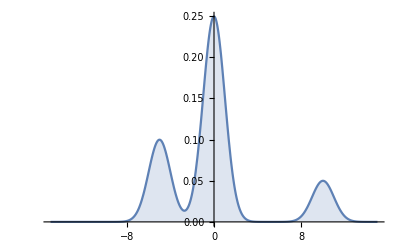

0

Root-7.45 × 10^-6Root[{-10+#1+5 ⅇ^(50-10 #1) #1+ⅇ^(-15 #1) (10 ⅇ^(75/2)+2 ⅇ^(75/2) #1)&,-7.4535730069815514699×10^-6}]-7.453573006981552e-6

750/(79 √79)

```mathematica
𝒟=MixtureDistribution[{5,2,1},{NormalDistribution[0,1],NormalDistribution[-5,1],NormalDistribution[10,1]}];
Plot[PDF[𝒟,x],{x,-15,15},Filling->Axis,PlotRange->All]
Mean[𝒟]
ArgMax[PDF[𝒟,x],x]
Skewness[𝒟]
```